```mathematica
size = 10;
points = Table[{Cos[((2*Pi)/size)*x],Sin[((2*Pi)/size)*x]},{x,1,size}];
```

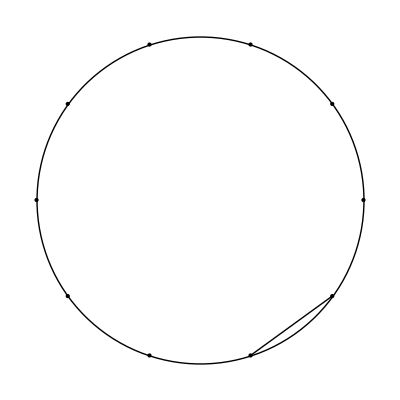

```mathematica
po = Graphics[Point[#]]&/@{points};
c = Graphics[Circle[]];
For[i=2,i<size,i++,
place = Mod[i+i,10];
lines =Graphics[Line[{ points[[i]],points[[place]] } ]];
]
Show[po,c, lines]
```